```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/rmtchem

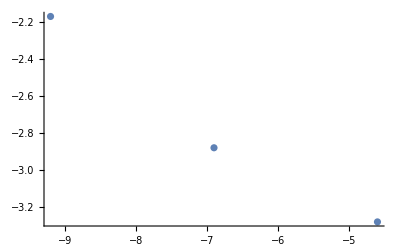

-4.43913-0.240638 x

```mathematica
vals=Table[Partition[Partition[BinaryReadList["data/2_"<>ToString[2000]<>"_"<>ToString[n]<>"gs.npy","Complex128"][[9;;-1]],2],2],{n,2,6,2}];
ListPlot[Transpose[{Log[{10^-2,10^-3,10^-4}],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,3}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,3}]]]}]]
Fit[Transpose[{Log[{10^-2,10^-3,10^-4}],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,3}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,3}]]]}],{1,x},x]
```

```mathematica
Transpose[{Log[{10^-2,10^-3,10^-4}],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,3}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,3}]]]}]
```

{{-Log[100],-3.27955},{-Log[1000],-2.87968},{-Log[10000],-2.17137}}

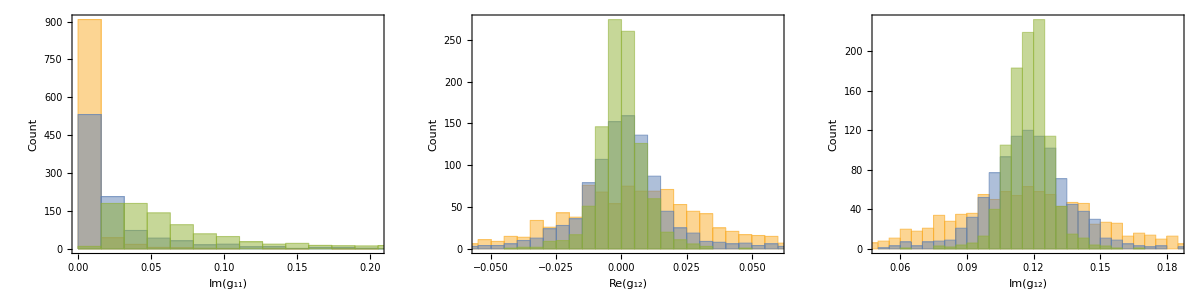
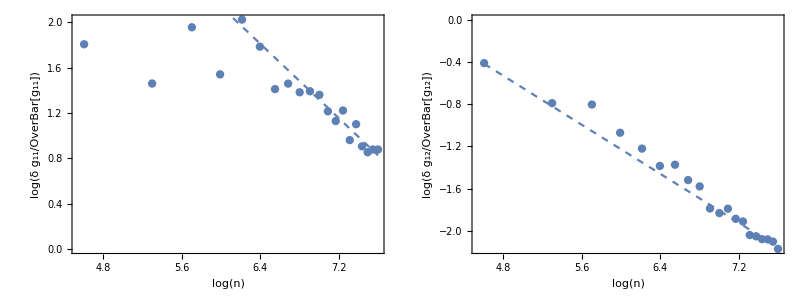

z=i.pdf

```mathematica
vals1=Partition[Partition[BinaryReadList["data/2_100_6gs.npy","Complex128"][[9;;-1]],2],2];
vals2=Partition[Partition[BinaryReadList["data/2_500_6gs.npy","Complex128"][[9;;-1]],2],2];
vals3=Partition[Partition[BinaryReadList["data/2_2000_6gs.npy","Complex128"][[9;;-1]],2],2];
p1=Grid[{{Histogram[{Im[vals1[[All,1,1]]],Im[vals2[[All,1,1]]],Im[vals3[[All,1,1]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"11"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Re[vals1[[All,1,2]]],Re[vals2[[All,1,2]]],Re[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Re[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Im[vals1[[All,1,2]]],Im[vals2[[All,1,2]]],Im[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250]}}];
vals=Table[Partition[Partition[BinaryReadList["data/2_"<>ToString[n]<>"_6gs.npy","Complex128"][[9;;-1]],2],2],{n,100,2000,100}];
f1=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,10,20}]]]}],{1,x},x];
f2=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,10,20}]]]}],{1,x},x];
p2=Grid[{{Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"11"],"/",OverBar[Subscript[g,"11"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f1,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f1,14],ImageScaled[{0.7,0.75}]]}],Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"12"],"/",OverBar[Subscript[g,"12"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f2,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f2,14],ImageScaled[{0.7,0.75}]]}]}}];
p=Grid[{{p1},{p2}}]
Export["z=i.pdf",p]
```

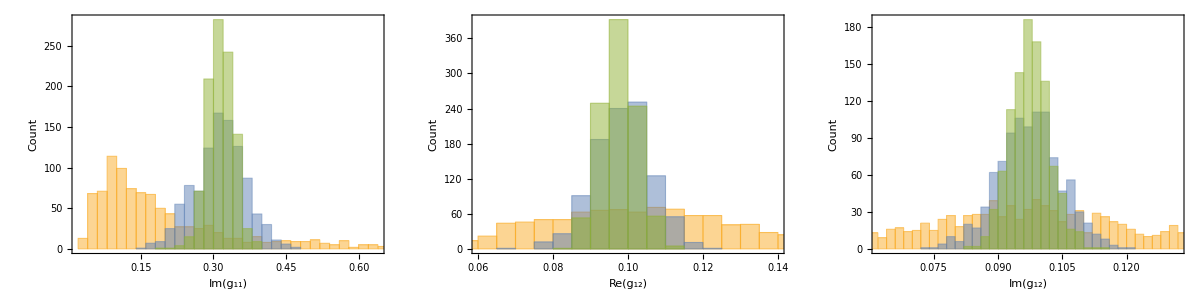
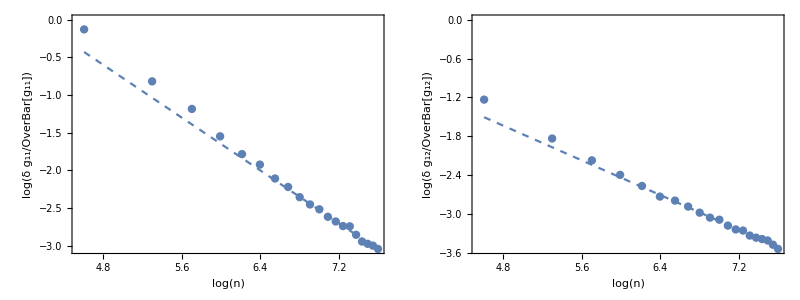

1i.pdf

```mathematica
vals1=Partition[Partition[BinaryReadList["data/2_100_3gs.npy","Complex128"][[9;;-1]],2],2];
vals2=Partition[Partition[BinaryReadList["data/2_500_3gs.npy","Complex128"][[9;;-1]],2],2];
vals3=Partition[Partition[BinaryReadList["data/2_1000_3gs.npy","Complex128"][[9;;-1]],2],2];
p1=Grid[{{Histogram[{Im[vals1[[All,1,1]]],Im[vals2[[All,1,1]]],Im[vals3[[All,1,1]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"11"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Re[vals1[[All,1,2]]],Re[vals2[[All,1,2]]],Re[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Re[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250],Histogram[{Im[vals1[[All,1,2]]],Im[vals2[[All,1,2]]],Im[vals3[[All,1,2]]]},Axes->False,Frame->True,FrameLabel->{Im[Subscript[g,"12"]],"Count"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->250]}}];
vals=Table[Partition[Partition[BinaryReadList["data/2_"<>ToString[n]<>"_3gs.npy","Complex128"][[9;;-1]],2],2],{n,100,2000,100}];
f1=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,10,20}]]]}],{1,x},x];
f2=Fit[Transpose[{Log[Table[i,{i,1000,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,10,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,10,20}]]]}],{1,x},x];
p2=Grid[{{Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,1]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,1]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"11"],"/",OverBar[Subscript[g,"11"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f1,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f1,14],ImageScaled[{0.7,0.75}]]}],Show[ListPlot[Transpose[{Log[Table[i,{i,100,2000,100}]],Log[Abs[Table[Variance[vals[[i,All,1,2]]]^(1/2),{i,1,20}]]/Abs[Table[Mean[vals[[i,All,1,2]]],{i,1,20}]]]}],ImageSize->300,Axes->False,Frame->True,FrameLabel->{Log[n],Log[DisplayForm[RowBox[{δ Subscript[g,"12"],"/",OverBar[Subscript[g,"12"]]}]]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]],Plot[f2,{x,Log[100],Log[2000]},PlotStyle->Directive[Dashed]],Epilog->{Inset[Style[f2,14],ImageScaled[{0.7,0.75}]]}]}}];
p=Grid[{{p1},{p2}}]
Export["1i.pdf",p]
```

## Regular random matrices

101

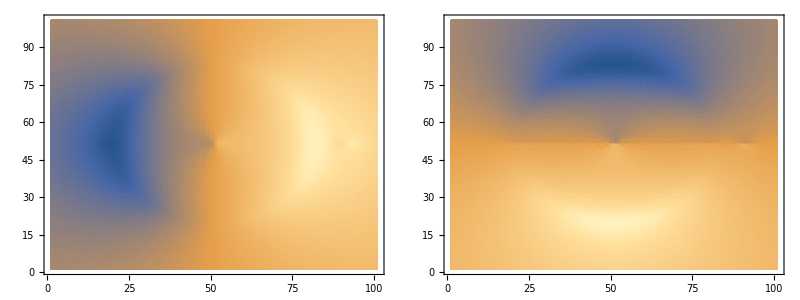

InterpolatingFunction[…]

InterpolatingFunction[…]

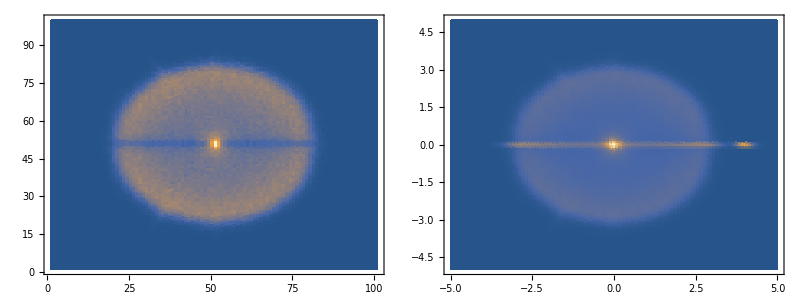

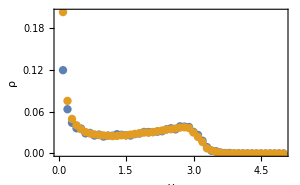

```mathematica
filebase="data/2_100_1";
n=Length[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2]]^(1/2)
max=5;
gvals=Partition[Partition[Partition[BinaryReadList[filebase<>"g.npy","Complex128"][[9;;-1]],2],2],n];Grid[{{ListDensityPlot[Transpose[Re[gvals[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0],
ListDensityPlot[Transpose[Im[gvals[[All,All,2,1]]]],ImageSize->300,InterpolationOrder->0]}}]
gr=Interpolation[Flatten[Table[{-max+2*max/(n-1)*(i-1),-max+2*max/(n-1)*(j-1),Re[gvals[[i,j,2,1]]]},{j,Complement[Range[n],{(n-1)/2+1}]},{i,Complement[Range[n],{(n-1)/2+1}]}],1]]
gi=Interpolation[Flatten[Table[{-max+(2*max)/(n-1)*(i-1),-max+(2*max)/(n-1)*(j-1),Im[gvals[[i,j,2,1]]]},{j,Complement[Range[n],{(n-1)/2+1}]},{i,Complement[Range[n],{(n-1)/2+1}]}],1]]

c2=Partition[BinaryReadList[filebase<>".npy","Real64"][[17;;-1]],n];
Grid[{{ListDensityPlot[Join[Transpose[c2][[1;;(n-1)/2]],Transpose[c2][[(n-1)/2+2;;n]]],ImageSize->300,InterpolationOrder->0,PlotRange->All],ListDensityPlot[Flatten[Table[{x,y,(Derivative[1,0][gr][x,y]-Derivative[0,1][gi][x,y])/(2*Pi)},{x,-max,max,2*max/n},{y,-max,max,2*max/n}],1],ImageSize->300,PlotRange->All]}}]
ListPlot[{Transpose[{max*Range[(n-1)/2]/((n-1)/2),Transpose[c2][[(n-1)/2+2;;n,(n-1)/2+1]]}],Table[{Y,Evaluate[D[gr[x,y],x]-D[gi[x,y],y]]/(2*Pi)}/.{x->0,y->Y},{Y,max/((n-1)/2),max,max/((n-1)/2)}]},ImageSize->300,InterpolationOrder->0,PlotRange->All,Axes->False,Frame->True,FrameLabel->{y,ρ},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]]]
```

data/test

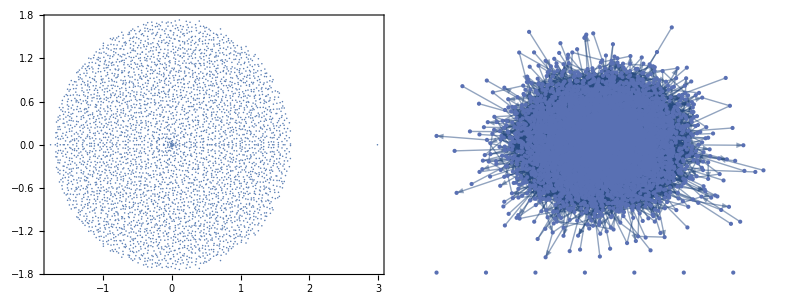

{0,10}

{0,11}

```mathematica
filebase="data/test"
mat=BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]];
n=Length[mat]^(1/2);
mat=Partition[mat,n];
evals=Partition[BinaryReadList[filebase<>"evals.npy","Real64"][[17;;-1]],2];
Grid[{{ListPlot[evals,ImageSize->300,AspectRatio->1,Axes->False,Frame->True,LabelStyle->Directive[16]],GraphPlot[AdjacencyGraph[mat/.u_/;Abs[u]>0->1/.(0.)->0],ImageSize->300]}}]
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@mat)
{Min[#],Max[#]}&@(Count[#,u_/;u≠0.]&/@Transpose[mat])
```

```mathematica
Length[Length/@components]
```

571

{563.673,Null}

-Graphics-

stack.png

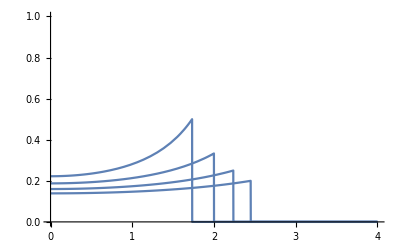

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];
c3=BinaryReadList["data/3.npy","Real64"][[17;;-1]];
c3=Transpose[Partition[c3,Length[c3]^(1/2)]];
c4=BinaryReadList["data/4.npy","Real64"][[17;;-1]];
c4=Transpose[Partition[c4,Length[c4]^(1/2)]];
c5=BinaryReadList["data/5.npy","Real64"][[17;;-1]];
c5=Transpose[Partition[c5,Length[c5]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;
AbsoluteTiming[{raster2,raster3,raster4,raster5}={Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c3[[1;;Floor[Length[c3]/2]]],c3[[Floor[Length[c3]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c4[[1;;Floor[Length[c4]/2]]],c4[[Floor[Length[c4]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300],Rasterize[ListDensityPlot[Join[c5[[1;;Floor[Length[c5]/2]]],c5[[Floor[Length[c5]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->All,Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]};]
p=Rasterize[Plot3D[{0,2,4,6},{x,-10,10},{y,-10,10},Mesh->None,PlotRange->{{-8,8},{-8,8},{0,6}},PlotStyle->{Directive[Texture[raster2]],Directive[Texture[raster3]],Directive[Texture[raster4]],Directive[Texture[raster5]]},Lighting->{"Ambient",White},Boxed->False,Axes->False,Background->None,ImageSize->300,ViewPoint->{-12,0,2},AspectRatio->2,ViewAngle->0.065],ImageResolution->300];
Rotate[p,-Pi/2]
Export["stack.png",Rotate[p,-Pi/2]]
```

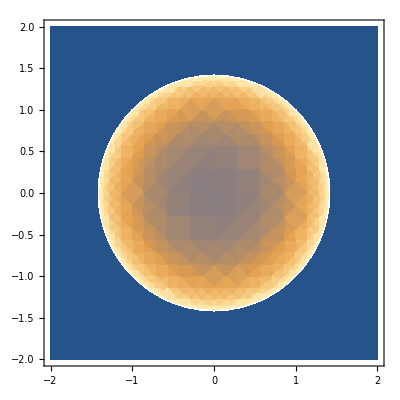

```mathematica
c=2;
DensityPlot[If[x^2+y^2<c,(c-1)*(c/(c^2-(x^2+y^2)))^2,0],{x,-c,c},{y,-c,c},PlotRange->All]
```

```mathematica
c2=BinaryReadList["data/2.npy","Real64"][[17;;-1]];
c2=Transpose[Partition[c2,Length[c2]^(1/2)]];

scale=Max[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]]/10;
offset=0.3*Median[Cases[Flatten[Join[c2[[1;;Floor[Length[c2]/2]]],c2[[Floor[Length[c2]/2]+2;;-1]]]],u_/;u>100]];
cf=If[#<1,White,ColorData["M10DefaultDensityGradient"][(#-offset)/(scale-offset)]]&;

p=Rasterize[ListDensityPlot[Join[c2[[1;;Floor[Length[c2]/2]]],{c2[[Floor[Length[c2]/2]]]+c2[[2+Floor[Length[c2]/2]]]}/2,c2[[Floor[Length[c2]/2]+2;;-1]]],InterpolationOrder->1,ImageSize->300,PlotRange->{{100,400},{100,400}},Frame->False,ColorFunctionScaling->False,ColorFunction->cf],ImageResolution->300]
Export["spectrum.png",p]
```

-Graphics-

spectrum.png

## Chemical reaction networks

data/test

{100,500}

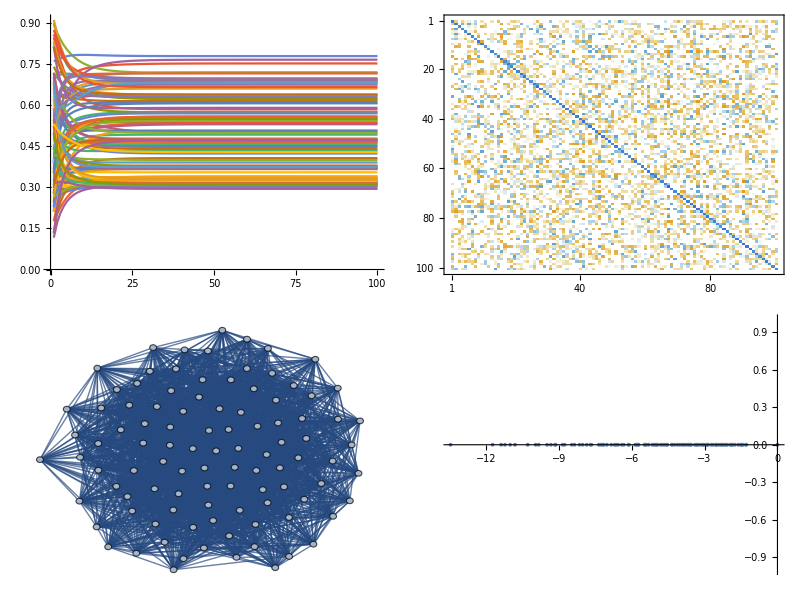

```mathematica
filebase="data/test"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

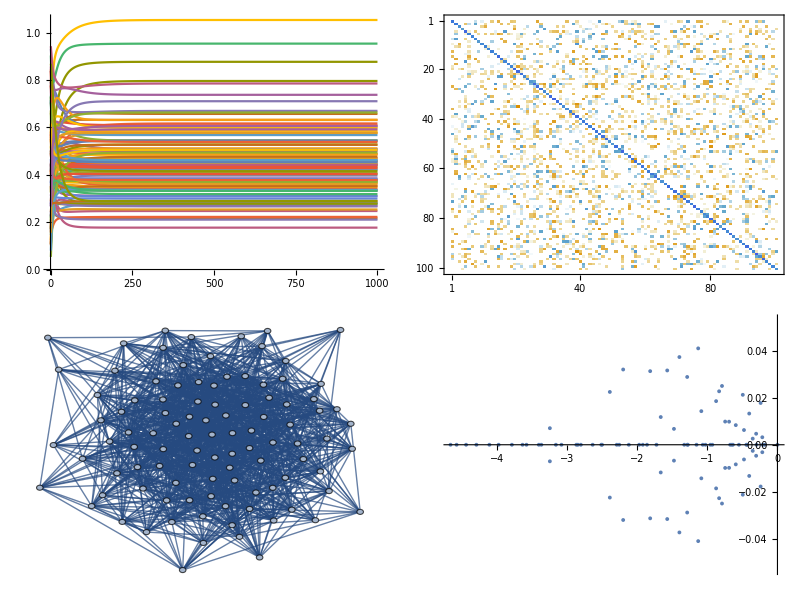

graph2.pdf

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
Export["graph2.pdf",AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300]]
```

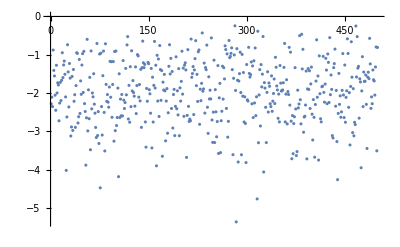

```mathematica
ListPlot[Diagonal[mat]]
```

```mathematica
filebase="data/irreversible2"
{n,nr}=Import[filebase<>"out.dat"][[1]]
X=Transpose[Partition[BinaryReadList[filebase<>"X.npy","Real64"][[17;;-1]],n]];
nu=Partition[BinaryReadList[filebase<>"nu.npy","Real64"][[17;;-1]],n];
eta=Partition[BinaryReadList[filebase<>"eta.npy","Real64"][[17;;-1]],n];
mat=Partition[BinaryReadList[filebase<>"mat.npy","Real64"][[17;;-1]],n];
adj=mat/.u_/;Abs[u]>0->1/.(0.)->0;
Grid[{{ListPlot[X,PlotRange->All,Joined->True,ImageSize->300],MatrixPlot[mat,ImageSize->300]},{AdjacencyGraph[adj-DiagonalMatrix[Diagonal[adj]],ImageSize->300],ListPlot[{Re[#],Im[#]}&/@Eigenvalues[mat],ImageSize->300]}}]
```

data/irreversible2

{100,250}

-Graphics-